```mathematica
FinancialData["GE"]
```

25.91

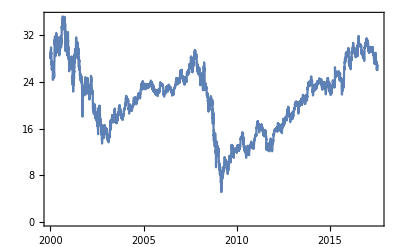

```mathematica
DateListPlot[FinancialData["GE","Jan. 1, 2000"]]
```

```mathematica
FinancialData["EUR/USD"]
```

1.1659

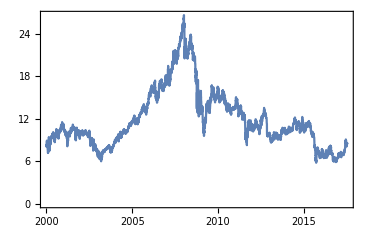

```mathematica
DateListPlot[FinancialData["F:EOAN","Jan. 1, 2000"]]
```

```mathematica
InteractiveTradingChart[{"F:EOAN",{{2009,1,1},{2009,12,31}}}]
```

```mathematica
CurrencyConvert[Quantity[13.25,"USDollars"],"Euros"]
```

11.36 €

```mathematica
fred=ServiceConnect["FederalReserveEconomicData"]
fred["SeriesSearch","Query"->"Gross Domestic Product","Frequency"->"Monthly",MaxItems->5]



proc=ItoProcess[ⅆx[t]==-x[t] ⅆt+Sqrt[1+x[t]^2] ⅆw[t],x[t],{x,1},t,w\[Distributed]WienerProcess[]]
```

ItoProcess[{{-x[t]},{{√(1+x[t]^2)}},x[t]},{{x},{1}},{t,0}]

```mathematica
RandomFunction[proc,{0.,5.,0.01}]
```

TemporalData[1]

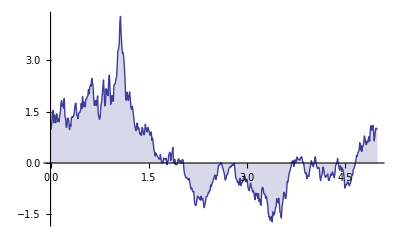

```mathematica
ListLinePlot[%,Filling->Axis]
```